## Setting up the problem

```mathematica
n=2;  (*Set the number of hysterons*)

(*Define symbolic variables*)
g=Symbol["g"];
vars=Table[Symbol["x"<>ToString[i]],{i,1,n}];  (*x1,x2,...,xn*)

(*Define the coefficients for each equation*)

coeffs=Table[{Symbol["a"<>ToString[i]],Symbol["b"<>ToString[i]],Symbol["c"<>ToString[i]],Symbol["d"<>ToString[i]],Table[Symbol["k"<>ToString[i]<>ToString[j]],{j,1,n}]},{i,1,n}];

(*Define the equations with interaction terms*)
equations=Table[coeffs[[i,1]] vars[[i]]^3+coeffs[[i,2]] vars[[i]]^2+coeffs[[i,3]] vars[[i]]+coeffs[[i,4]] g-Sum[coeffs[[i,5,j]] (vars[[j]]-vars[[i]]),{j,1,n}]-coeffs[[i,5,i]] (vars[[i]]-vars[[i]]),{i,1,n}];
jacobian=Table[Table[D[equations[[i]],vars[[j]]],{j,1,n}],{i,1,n}];(*Compute the Jacobian matrix:the partial derivatives of each equation w.r.t each variable*)
{a1,b1,c1,d1,k11,k12,a2,b2,c2,d2,k21,k22}={vv1,1,-4.2,-1,0,-3,2.1,1.2,-4.6,-1.2,-3,0};
equations1[var_,gg_]:=((equations)/.{vv1->var,g->gg})(*Constraint equations*)
equations2[var_]:=(Join[equations,{Det@jacobian}]/.vv1->var)(*Constraint equations + detJ=0*)
solutions[var_,g_]:=solutions[var,g]:=vars/.NSolve[equations1[var,g]==0,vars,Reals]
bifurcationpoints[var_]:=Select[Join[vars,{g}]/.NSolve[equations2[var]==ConstantArray[0,n+1],Join[vars,{g}],Reals],(Abs[#[[1]]]<3&&Abs[#[[2]]]<3)&]
equationsg[var_]:=((D[equations,g])/.vv1->var)
replacementrule[var_,i_]:=Thread[Join[vars,{g}]->bifurcationpoints[var][[i]]]
eigensystem[i_,var_]:=Chop@SortBy[Eigensystem[jacobian/.replacementrule[var,i]/.vv1->var],Abs[#[[1]]]&](*Finds the eigenvalues and eigenvectors and sorts so that the 0 eigenvalue is last*)
condition1[i_,var_]:=eigensystem[i,var][[2,-1]].equationsg[var]
seconderivatives[var_]:=MapThread[D[D[#1,#2],#2]&,{equations1[var,g],vars}]
condition2[i_,var_]:=(eigensystem[i,var][[2,-1]].(Table[seconderivatives[var][[j]]*(eigensystem[i,var][[2,-1,j]])^2,{j,1,n}]))(*Fix this to be for general number of hysterons*)(*When calling this, need to replace the vars with the values at the bifurcation point using Thread.*)
(*{vv1,1,-4.2,-1,0,-3,2.1,1.2,-4.6,-1.2,-3,0};*)
```

#### Dynamics

```mathematica
dynamicsvariables=#[t]&/@vars;
dynamicsvariablesderivates=D[#,t]&/@dynamicsvariables;
initconditions=dynamicsvariables/.t->0;
replacementrule2=Thread[vars->(#[t]&/@vars)];
check1[var_,i_]:=Drop[eigensystem[i,var][[1]],-1](*Will use this to make sure all eigenvalues are positive for stability*)
check2[var_,i_]:=Drop[bifurcationpoints[var][[i]],-1](*Will use this to find the hysteron states at that bifurcation point*)
check3[var_,i_]:=condition2[i,var]/.Thread[vars->Drop[bifurcationpoints[var][[i]],-1]](*This checks whether the point was created or annihilated depending on the sign of condition2 value*)
checktable[var_]:=Table[{check1[var,i],check2[var,i],check3[var,i],bifurcationpoints[var][[i,3]]},{i,1,Length@bifurcationpoints[var]}]
checktabl1[var_]:=#[[1]]&/@checktable[var]
checktabl2[var_]:=#[[2]]&/@checktable[var]
checktabl3[var_]:=#[[3]]&/@checktable[var]
firstcheck[var_]:=Table[AllTrue[checktabl1[var][[i]],#>0&],{i,1,Length@bifurcationpoints[var]}](*Here save a list first so you don't have to run checktabl1 so many times. That's the culprit of taking long.*)
hysteronstates[var_]:=Map[If[#>=0,1,0]&,checktabl2[var],{2}]
newlist[var_]:=Select[Transpose[{firstcheck[var],hysteronstates[var],checktabl3[var],bifurcationpoints[var]}],#[[1]]===True&](*This function groups all the conditions for each hysterons and removes the unstable states completely. To keep them in, we'd simply have to remove the Select function in this case.*)
newlist2[var_]:=MapAt[ToString,Select[Transpose[{firstcheck[var],hysteronstates[var],checktabl3[var]}],#[[1]]===True&],{All,2}]
possiblestates[var_]:=Union[newlist[var][[All,2]]]
randomcolors[var_]:=RandomColor[Length@possiblestates[var]](*Need to revisit this because I can get the same color for two different states*)
coords[var_]:={#[[4,-1]],var}&/@newlist[var]
```

## Run the code here (n hysterons)

```mathematica
vv1lims={.5,3.5};
tolerance=10^-4;
crossingpoints=Sort@DeleteDuplicates[vv1/.NSolve[equations==0&&(equations/.{x1->x11,x2->x22})==0&&Det@jacobian==0&&(Det@jacobian/.{x1->x11,x2->x22})==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x11]<3&&Abs[x22]<3&&vv1lims[[1]]<=vv1<=vv1lims[[2]],{x1,x2,x11,x22,g,vv1},Reals],(Norm[#1-#2]<tolerance&)];
cusppoints=Sort[vv1/.NSolve[equations==0&&Det@jacobian==0&&(-D[equations[[2]],x1])/D[equations[[1]],x1](D[D[equations[[1]],x1],x1])+(D[D[equations[[2]],x2],x2])==0&&Abs[x1]<3&&Abs[x2]<3&&vv1lims[[1]]<=vv1<=vv1lims[[2]],{x1,x2,g,vv1},Reals]];
cd2=Sort@Join[crossingpoints,cusppoints];
extendedMidpoints[list_]:=Module[{first,last,extendedList,offset},offset[n1_,n2_]:=0.05 (n2-n1);(*5% offset of the difference*)first=list[[1]]-offset[list[[1]],list[[2]]];(*Slightly smaller first number*)last=list[[-1]]+offset[list[[-2]],list[[-1]]];(*Slightly larger last number*)extendedList=Prepend[Append[list,last],first];
Mean/@Partition[extendedList,2,1]]
pointstocheck=extendedMidpoints[cd2]
```

{0.516344,1.01877,1.70394,1.97398,2.03741,2.18018,2.80511,3.31145}

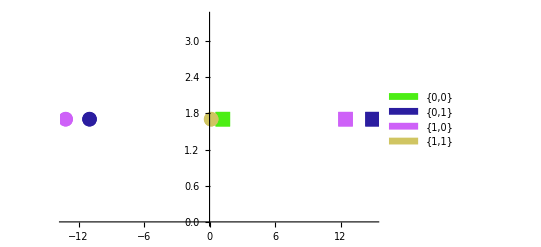

-Graphics-

```mathematica
Clear[var];
vvar=pointstocheck[[3]];
var=vvar;(*Set the variable here*)
currentnewlist=newlist[var];
uniquestates=possiblestates[var];
currentcolors=RandomColor[Length@uniquestates];
stateColorMap=AssociationThread[uniquestates->currentcolors];
newlistWithColors=Map[Function[{item},Append[item,stateColorMap[item[[2]]]]],currentnewlist];
shapes=If[#[[3]]>0,{"■",15},{"●",15}]&/@newlistWithColors;
colorsordered=#[[5]]&/@newlistWithColors;
legendLabels=SwatchLegend[currentcolors,uniquestates];
ListPlot[List/@({#[[4,-1]],var}&/@newlistWithColors),PlotStyle->colorsordered,PlotMarkers->shapes,PlotLegends->legendLabels,PlotRange->All]

creationpoints=#[[2]]&/@Select[{#[[3]],#[[4]]}&/@currentnewlist,(-1)^n*#[[1]]<0&];
annihilationpoints=#[[2]]&/@Select[{#[[3]],#[[4]]}&/@currentnewlist,(-1)^n*#[[1]]>0&];
Clear[var];
pars=Table[Symbol["x0"<>ToString[i]],{i,1,n}];  (*x1,x2,...,xn*)
parameters=Flatten[{var,g,pars}];
dynamicssoln=ParametricNDSolve[Flatten@{Thread[-dynamicsvariablesderivates==(equations1[var,g]/.replacementrule2)],Thread[initconditions==(#&/@Drop[parameters,2])]},vars,{t,0,100},parameters];
sollist[parameters_,t_]:=(#[Sequence@@parameters][t]&/@vars)/. dynamicssoln
eps=.005;
{Length@creationpoints,Length@annihilationpoints};(*The limit of what i can be when running the dynamics*)
setparameter1[var_,i_]:=Join[{var,annihilationpoints[[i,-1]]+eps},Table[annihilationpoints[[i,j]],{j,1,n}]]
setparameter2[var_,i_]:=Join[{var,creationpoints[[i,-1]]-eps},Table[creationpoints[[i,j]],{j,1,n}]]
solutionsinc[var_,i_]:=sollist[parameters,100]/.Thread[parameters->setparameter1[var,i]]
solutionsdec[var_,i_]:=sollist[parameters,100]/.Thread[parameters->setparameter2[var,i]]
uptransitions[var_]:=(Table[{Table[annihilationpoints[[i,j]],{j,1,n}],Flatten@solutionsinc[var,i]},{i,1,Length@annihilationpoints}]/. x_Real:>If[x>0,1,0])
downtransitions[var_]:=(Table[{Table[creationpoints[[i,j]],{j,1,n}],Flatten@solutionsdec[var,i]},{i,1,Length@creationpoints}]/. x_Real:>If[x>0,1,0])
var=vvar;
edges=Join[Table[uptransitions[var][[i,1]]->uptransitions[var][[i,2]],{i,1,Length@annihilationpoints}],Table[downtransitions[var][[i,1]]->downtransitions[var][[i,2]],{i,1,Length@creationpoints}]];
Graph[edges,VertexLabels->(v_Real:>Style[v,FontSize->12,Background->LightGray]),GraphStyle->"NameLabeled",VertexStyle->White,VertexSize->Medium,EdgeStyle->GrayLevel[0],GraphLayout->"SpringEmbedding"]
```